```mathematica
(*REc на отрезке от i-1 до i*)
Fi[x_]:=(x-r1i)/(ri-r1i);
Integrate[polsRR((lambda + 2 mu)*D[Fi[r],r]r +lambda Fi[r]) + polsFF(lambda D[Fi[r],r]r +(lambda + 2 mu) Fi[r]),{r,r1i,ri}]//FullSimplify
Fi[x_]:=(x-ri1)/(ri-ri1);

Integrate[PolsRR((lambda + 2 mu)*D[Fi[r],r]r +lambda Fi[r]) + PolsFF(lambda*D[Fi[r],r]r +(lambda + 2 mu)Fi[r]),{r,ri,ri1}]//FullSimplify
```

mu (-polsFF+polsRR) r1i+(lambda+mu) (polsFF+polsRR) ri

-((lambda+mu) (PolsFF+PolsRR) ri)+mu (PolsFF-PolsRR) ri1

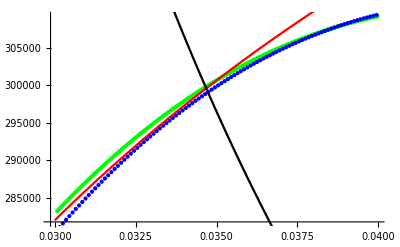

```mathematica
(*ClearAll["Global`*"];*)
SetDirectory[NotebookDirectory[]];
numSolution=ReadList["pols.txt", {Number, Number}];
settings = ReadList["polsSettings.txt",Number];
h =settings[[1]];a =settings[[2]];b =settings[[3]];
Pa =settings[[4]];
Pb=settings[[5]];
e=settings[[6]];
nu=settings[[7]];
T = settings[[8]];
M=settings[[9]];
n =3;
p=Pa;
r1=a;r2=b;
exactSigmaRR[r_]:=(p r1^(2/n))/(r2^(2/n)-r1^(2/n))(1- r2^(2/n)/r^(2/n))
sigmaRRPlot=Plot[exactSigmaRR[r],{r,a,b}];
exactSigmaFF[r_]:=(p r1^(2/n))/(r2^(2/n)-r1^(2/n))(1+(2-n)/n r2^(2/n)/r^(2/n))
sigmaFFPlot=Plot[exactSigmaFF[r],{r,a,b},PlotStyle->Red];
sigmaRRPlot=Plot[exactSigmaRR[r],{r,a,b},PlotStyle->Red];
numSigmaFF=Import["sigmaFFPols.txt","Table"];
numTable={};
For[i =1,i<Length[numSigmaFF],i++,
r=a+h/2;num={};
For[k=0,k<Length[numSigmaFF[[i]]],k++,
r+=h;
num=Append[num,{r,numSigmaFF[[i]][[k+1]]}]];
numTable=Append[numTable,num]
]
exactSigmaFFUpr[h_]:= (Pa  a^2-Pb  b^2)/(b^2-a^2)+ (a^2 b^2)/h^2 * (Pa -Pb)/(b^2-a^2);
sigmaFFPlotUpr=Plot[exactSigmaFFUpr[r],{r,a,b},PlotStyle->Black];
exactSigmaRRUpr[h_]:= (Pa  a^2-Pb  b^2)/(b^2-a^2)- (a^2 b^2)/h^2 * (Pa -Pb)/(b^2-a^2);
sigmaRRPlotUpr=Plot[exactSigmaRRUpr[r],{r,a,b},PlotStyle->Black];
(*gif=Animate[
Show[ListPlot[numTable[[i]]],sigmaFFPlotUpr,sigmaFFPlot],{i,1,M-1,1}]*)
(*Export["SigmaFF.gif",gif]*)
plot200FF= ListPlot[numTable[[Length[numTable]]], PlotStyle->{Green, PointSize->Medium}];
Show[plot200FF,plot100FF,sigmaFFPlot,sigmaFFPlotUpr]
```

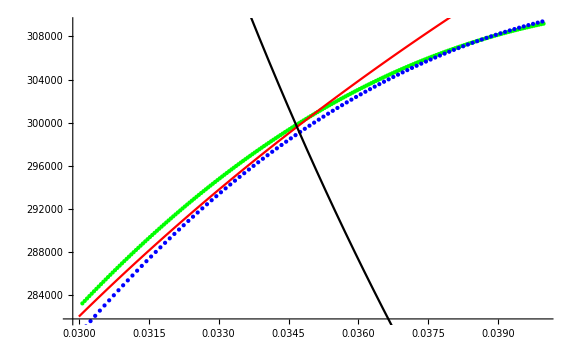

```mathematica
Show[%440,ImageSize->Large]
```

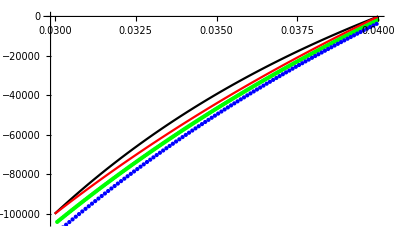

```mathematica
numSigmaRR=Import["sigmaRRPols.txt","Table"];
numTable={};
For[i =1,i<Length[numSigmaRR]+1,i++,
r=a+h/2;num={};
For[k=0,k<Length[numSigmaRR[[i]]],k++,
r+=h;
num=Append[num,{r,numSigmaRR[[i]][[k+1]]}]];
numTable=Append[numTable,num]
]

(*gif=Animate[
Show[sigmaRRPlot,ListPlot[numTable[[i]]],sigmaRRPlotUpr],{i,1,M-1,1}]*)
(*Export["SigmaRR.gif",gif]*)
plot200RR = ListPlot[numTable[[Length[numTable]]], PlotStyle->{Green, PointSize->Medium}];
Show[plot200RR,plot100RR,sigmaRRPlotUpr,sigmaRRPlot]
```

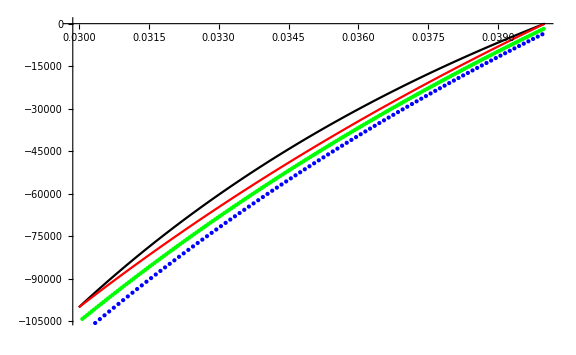

```mathematica
Show[%445,ImageSize->Large]
```

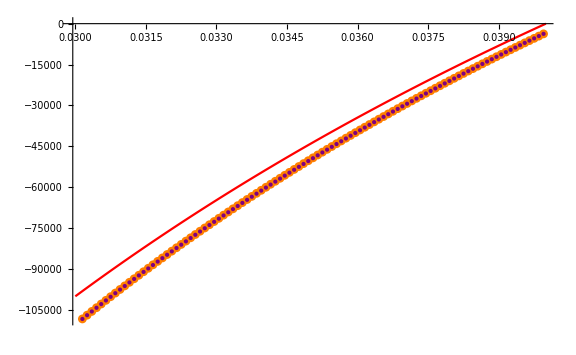

```mathematica
Show[%359,ImageSize->Large]
```

```mathematica
Show[%353,ImageSize->Large]
```

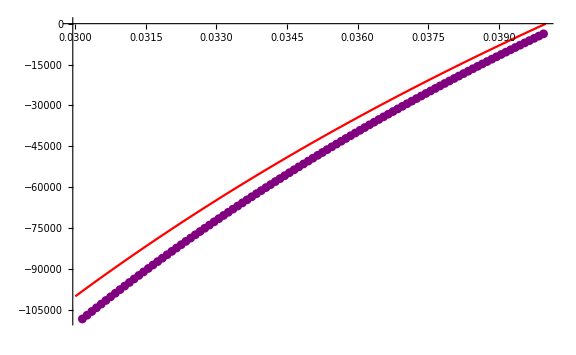

```mathematica
Show[%280,ImageSize->Large]
```

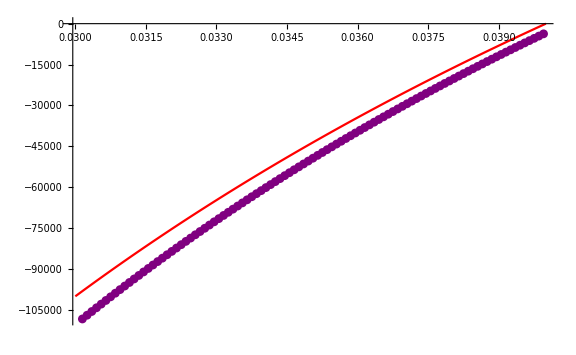

```mathematica
Show[%268,ImageSize->Large]
```

```mathematica
Show[%247,ImageSize->Large]
```

-Graphics-

```mathematica
Show[%231,ImageSize->Large]
```

-Graphics-